{{m3→c/(3 ε),m2→0,m1→0,m0→0,r1→-c ε,r0→(c ε^2)/3}}

y_L(x;c,ε) = 0

y_L'(x;c,ε) = 0

y_L''(x;c,ε) = 0

y_M(x;c,ε) = c\ x^3/3\ ε

y_M'(x;c,ε) = c\ x^2/ε

y_M''(x;c,ε) = 2\ c\ x/ε

y_R(x;c,ε) = c\ x^2 - c\ x\ ε + c\ ε^2/3

y_R'(x;c,ε) = 2\ c\ x - c\ ε

y_R''(x;c,ε) = 2\ c

y'_thresh(;c,ε) = c\ ε

inverting y_M...

{{x→-((-3)^(1/3) y^(1/3) ε^(1/3))/c^(1/3)},{x→(3^(1/3) y^(1/3) ε^(1/3))/c^(1/3)},{x→(y^(1/3) ε^(1/3) Root[-3+#1^3&,3])/c^(1/3)}}

inverting y_R...

{{x→(3 c ε-√3 √(c (12 y-c ε^2)))/(6 c)},{x→(3 c ε+√3 √(c (12 y-c ε^2)))/(6 c)}}

inverting y'_M...

{{x→-(√y √ε)/(√c)},{x→(√y √ε)/(√c)}}

inverting y'_R...

{{x→(y+c ε)/(2 c)}}

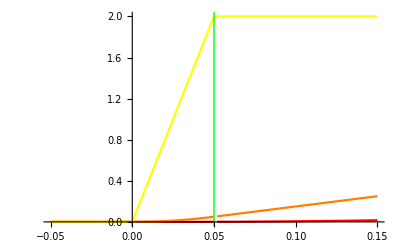

```mathematica
ClearAll["`*"];

yL[x_]:=0;
yR[x_]:=c x^2+r1 x+r0;
yM[x_]:=m3 x^3+m2 x^2+m1 x+m0;

bcL1=yM[0]==yL[0];
bcL2=yM'[0]==yL'[0];
bcL3=yM''[0]==yL''[0];
bcR1=yM[ε]==yR[ε];
bcR2=yM'[ε]==yR'[ε];
bcR3=yM''[ε]==yR''[ε];

sols=Solve[{bcL1,bcL2,bcL3,bcR1,bcR2,bcR3},{m3,m2,m1,m0, r1,r0}]

Set@@@sols[[1]];

StringForm["y_L(x;c,ε) = ``" ,yL[x]]
StringForm["y_L'(x;c,ε) = ``" ,yL'[x]]
StringForm["y_L''(x;c,ε) = ``" ,yL''[x]]

StringForm["y_M(x;c,ε) = ``" ,yM[x]]
StringForm["y_M'(x;c,ε) = ``" ,yM'[x]]
StringForm["y_M''(x;c,ε) = ``" ,yM''[x]]

StringForm["y_R(x;c,ε) = ``" ,yR[x]]
StringForm["y_R'(x;c,ε) = ``" ,yR'[x]]
StringForm["y_R''(x;c,ε) = ``" ,yR''[x]]

yLinterval[x_]:={yL[x],x≤0};
yMinterval[x_]:={yM[x],0<x≤ε};
yRinterval[x_]:={yR[x],ε<x};
y[x_]:=Piecewise[{yLinterval[x],yMinterval[x],yRinterval[x]}]

StringForm["y'_thresh(;c,ε) = ``" ,yM'[ε]]

StringForm["inverting y_M..."]
Solve[{yM[x]==y},x]//FullSimplify
StringForm["inverting y_R..."]
Solve[{yR[x]==y},x]//FullSimplify
StringForm["inverting y'_M..."]
Solve[{yM'[x]==y},x]//FullSimplify
StringForm["inverting y'_R..."]
Solve[{yR'[x]==y},x]//FullSimplify

c=1;ε=.05;
yplot=Plot[y[x],{x,-ε,3ε},PlotStyle->Red];
dydxplot=Plot[y'[x],{x,-ε,3ε},PlotStyle->Orange];
d2ydx2plot=Plot[y''[x],{x,-ε,3ε},PlotStyle->Yellow];
epsbar=Plot[100 Sign[x-ε],{x,-ε,3ε},ExclusionsStyle->Green];
Show[yplot,dydxplot,d2ydx2plot,epsbar,PlotRange->{Automatic,{0,2c}}]
```

```mathematica
3^(1/3)
```

3^(1/3)

```mathematica
N[3^(1/3)]
```

1.44225

```mathematica
NumberForm[1.4422495703074083,15]
```

1.44224957030741